## Main Program

### Interface

#### Temporary Interface

```mathematica
interface[deltaT_,t_,r_,height_,dens_,fuel_,ρ0_,g0_]:=Module[{data={},v=0,h=0,mt=0},
data=rocket[deltaT,t,r,height,dens,fuel,ρ0,g0];
v=data[[1]];
h=data[[2]];
mt=data[[3]];
GraphicsRow[{SSRocket[r,height,{0,0,h}],Graphics[{Blue,Text[Style["Current Velocity: " <>ToString[v]<>" m/s",Large],{0,.3}],Text[Style["Current Altitude: " <>ToString[h]<>" m",Large],{0,0}],Text[Style["Current Mass: " <>ToString[mt]<>" Kg",Large],{0,-.3}]}]},0,ImageSize->800,AspectRatio->Full]
]
```

```mathematica
Manipulate[interface[.1,t,r,h,d,fm,ρ,g],
{{t,0,"Time"},0,500},
{{r,5,"Radius"},3,12},
{{h,110,"Height"},50,200},
{{d,20,"Material Density"},10,50},
{{fm,2500000,"Fuel Mass"},1500000,3500000},
{{ρ,1,"Atmospheric Pressure at Sea Level"},0,1},
{{g,9.8,"Gravitational Acceleration"},0,9.8}
]
```

#### Work-in-Progress Final Interface

```mathematica
PrimaryInterface:=DynamicModule[{currentMenu=1,t=0,DeltaT=0.5,r=5,rocketheight=110,density,fuelmass,ρ=1,g0=9.8,data={},v=0,h=0,mt=0,rocketpos={0,0,0},velocity,altitude,acceleration,gravity,pressure,mass,display={Text["Hi cruel world"]}},
data=rocket[Dynamic[DeltaT],Dynamic[t],Dynamic[r],Dynamic[rocketheight],Dynamic[density],Dynamic[fuelmass],Dynamic[ρ],Dynamic[g0]];
v=Dynamic[data[[1]]];
h=Dynamic[data[[2]]];
mt=Dynamic[data[[3]]];
rocketpos={0,0,Dynamic[h]};
velocity="Current Velocity: "<>ToString[Dynamic[v]]<>" m/s";
altitude="Current Altitude: "<>ToString[Dynamic[h]]<> " m";
acceleration="Current Acceleration: ";
gravity="Current Acceleration due to Gravity: "<>ToString[Dynamic[g0]]<>" m/s";
pressure="Current Atmospheric Pressure: "<>ToString[Dynamic[ρ]]<>" atm";
mass="Current Rocket Mass"<>ToString[Dynamic[mt]]<>" Kg";

Switch[Dynamic[currentMenu],
1,display={
Slider[Dynamic[DeltaT],{0.0001,5}],
Slider[Dynamic[t],{0,10000}],
Text[Dynamic[velocity]],
Text[Dynamic[altitude]],
Text[Dynamic[acceleration]],
Text[Dynamic[gravity]],
Text[Dynamic[pressure]],
Text[Dynamic[mass]]
},
2,display={
},
3,display={
}
];

Row[{SSRocket[r,rocketheight,rocketpos],
Column[{
PopupMenu[Dynamic[currentMenu],{1->"Main Menu",2->"Rocket Menu",3->"Planet Menu"}],
Dynamic[display]
}]
},ImageSize->800]
]
```

```mathematica
PrimaryInterface
```

### Animation Resources

#### Single Stage Rocket

```mathematica
SSRocket[r_,h_,pos_,θ_]:=Module[{noseconebasepos={0,0,0},noseconetoppos={0,0,0},stage1bottom={0,0,0},engine1bottom={0,0,0},engine1top={0,0,0},groundpos={},launchpad={},i,flame1point={0,0,0},flamelength=0,stage1pos={}},

(* Sets the positions of each of the stages and checks to see if they are clipping into the launchpad *)
stage1pos=pos;
If[stage1pos[[3]]<10,stage1pos[[3]]=10];

(* Creates the ground and launchpad *)
groundpos={{-r*5,-r*5,0},{-r*5,r*5,0},{r*5,r*5,0},{r*5,-r*5,0}};
launchpad=Table[{groundpos[[i,1]]/1.5,groundpos[[i,2]]/1.5,groundpos[[i,3]]},{i,1,4}];
launchpad=Join[launchpad,Table[{launchpad[[i,1]],launchpad[[i,2]],launchpad[[i,3]]+10},{i,1,4}]];

(* Defines the nosecone as 1/8th the overall height of the rocket *)
noseconebasepos[[3]]=stage1pos[[3]]+(h-(h/8));
noseconetoppos[[3]]=stage1pos[[3]]+h;

stage1bottom[[3]]=stage1pos[[3]]+(h/16);
engine1bottom[[3]]=stage1pos[[3]];
engine1top[[3]]=stage1pos[[3]]+(h/8);

(* Checks to see if the rocket is too close to the pad for the flame to display properly and if so, sets the flame length to the distance between the engine and the pad *)
If[4*(engine1top[[3]]-engine1bottom[[3]])<=engine1bottom[[3]]-launchpad[[5,3]],flamelength=4*(engine1top[[3]]-engine1bottom[[3]]),flamelength=engine1bottom[[3]]-launchpad[[5,3]]];
flame1point[[3]]=engine1bottom[[3]]-flamelength;


Graphics3D[{
Green,Polygon[groundpos],
Gray,Hexahedron[launchpad],
Rotate[{
Orange,Opacity[0.4],Cone[{engine1bottom,flame1point},r/1.5],Opacity[1],
FaceForm[RGBColor["#BCC6CC"]],Specularity[Gray,60],
Cone[{noseconebasepos,noseconetoppos},r],
Cylinder[{stage1bottom,noseconebasepos},r],
Cone[{engine1bottom,engine1top},r/1.5]},θ,{0,1,0},pos]
},ImageSize->Medium,Boxed->False]
]
```

```mathematica
Manipulate[SSRocket[5,100,{0,0,h},θ],{h,0,500},{θ,-π/2,π/2}]
```

#### Two Stage Rocket

```mathematica
DSRocket[stages_,θ_]:=Module[{noseconebasepos={0,0,0},noseconetoppos={0,0,0},stage2bottom={0,0,0},stageskirtbottom={0,0,0},stageskirttop={0,0,0},stage1bottom={0,0,0},engine1bottom={0,0,0},engine1top={0,0,0},engine2bottom={0,0,0},engine2top={0,0,0},groundpos={},launchpad={},i,flame1point={0,0,0},flamelength=0,flame2point={0,0,0},stage1pos={},stage2pos={},height=stages[[1,2]]+stages[[2,2]]},

(* Sets the positions of each of the stages and checks to see if they are clipping into the launchpad *)
stage1pos=stages[[1,3]];
stage2pos=stages[[2,3]];
If[stage1pos[[3]]<10,stage1pos[[3]]=10];
If[stage2pos[[3]]<10,stage2pos[[3]]=10];

(* Creates the ground and launchpad *)
groundpos={{-stages[[1,1]]*5,-stages[[1,1]]*5,0},{-stages[[1,1]]*5,stages[[1,1]]*5,0},{stages[[1,1]]*5,stages[[1,1]]*5,0},{stages[[1,1]]*5,-stages[[1,1]]*5,0}};
launchpad=Table[{groundpos[[i,1]]/1.5,groundpos[[i,2]]/1.5,groundpos[[i,3]]},{i,1,4}];
launchpad=Join[launchpad,Table[{launchpad[[i,1]],launchpad[[i,2]],launchpad[[i,3]]+10},{i,1,4}]];

(* Defines the nosecone as 1/8th the overall height of the rocket *)
noseconebasepos[[3]]=stage2pos[[3]]+(height-(height/8));
noseconetoppos[[3]]=stage2pos[[3]]+height;
(* Defines the bottom of stage two as the height of the first stage plus the height of the engine *)
stage2bottom[[3]]=stage2pos[[3]]+stages[[1,2]]+(stages[[2,2]]/16);
(* Defines the height of the engine as 1/8 the height of the second stage, but only half of this will be showing (The fuselage hides the top of the cone) *)
engine2top[[3]]=stage2pos[[3]]+stages[[1,2]]+(stages[[2,2]]/8);
engine2bottom[[3]]=stage2pos[[3]]+stages[[1,2]];
(* Defines the skirt between the two stages such that it covers the second stage engine *)
stageskirtbottom[[3]]=stage1pos[[3]]+stages[[1,2]];
stageskirttop[[3]]=stage1pos[[3]]+stages[[1,2]]+(stages[[2,2]]/6);
(* Defines the engine of the rocket similarly to the second stage *)
stage1bottom[[3]]=stage1pos[[3]]+(stages[[1,2]]/16);
engine1bottom[[3]]=stage1pos[[3]];
engine1top[[3]]=stage1pos[[3]]+(stages[[1,2]]/8);
(* Since the second stage will always be covered unless it has separated, the flame can be defined simply as a cone that is 4 times the length of the engine *)
flame2point[[3]]=engine2bottom[[3]]-4*(engine2top[[3]]-engine2bottom[[3]]);

(* Checks to see if the rocket is too close to the pad for the flame to display properly and if so, sets the flame length to the distance between the engine and the pad *)
If[4*(engine1top[[3]]-engine1bottom[[3]])<=engine1bottom[[3]]-launchpad[[5,3]],flamelength=4*(engine1top[[3]]-engine1bottom[[3]]),flamelength=engine1bottom[[3]]-launchpad[[5,3]]];
If[stage1pos[[3]]≠stage2pos[[3]],flame1point[[3]]=engine1bottom[[3]],
flame1point[[3]]=engine1bottom[[3]]-flamelength];

Graphics3D[{
Green,Polygon[groundpos],
Gray,Hexahedron[launchpad],
Rotate[{
Orange,Opacity[0.4],Cone[{engine1bottom,flame1point},stages[[1,1]]/1.5],
Cone[{engine2bottom,flame2point},stages[[2,1]]/1.5],
Opacity[1],
FaceForm[RGBColor["#BCC6CC"]],Specularity[Gray,60],
Cone[{noseconebasepos,noseconetoppos},stages[[2,1]]],
Tube[{stageskirtbottom,stageskirttop},{stages[[1,1]],stages[[2,1]]}],
Cone[{engine2bottom,engine2top},stages[[2,1]]/1.5],
Cylinder[{stage2bottom,noseconebasepos},stages[[2,1]]],
Cylinder[{stage1bottom,stageskirtbottom},stages[[1,1]]],
Cone[{engine1bottom,engine1top},stages[[1,1]]/1.5]},θ,{0,1,0},stage2pos]
},ImageSize->Medium,Boxed->False]
]
```

```mathematica
Manipulate[DSRocket[{{5,50,{0,0,h}},{3,40,{0,0,h}}},θ],{h,0,500},{θ,-π/2,π/2}]
```

#### Three Stage Rocket

```mathematica
TSRocket[stages_,θ_]:=
Module[{noseconebasepos={0,0,0},noseconetoppos={0,0,0},stage2bottom={0,0,0},interstagebot={0,0,0},interstagetop={0,0,0},stageskirtbottom={0,0,0},stageskirttop={0,0,0},stage1bottom={0,0,0},engine1bottom={0,0,0},engine1top={0,0,0},engine2bottom={0,0,0},engine2top={0,0,0},stage3bottom={0,0,0},engine3bottom={0,0,0},engine3top={0,0,0},groundpos={},launchpad={},i,flame1point={0,0,0},flamelength=0,flame2point={0,0,0},flame3point={0,0,0},stage1pos={},stage2pos={},stage3pos={},height=stages[[1,2]]+stages[[2,2]]+stages[[3,2]]},

(* Sets the positions of each of the stages and checks to see if they are clipping into the launchpad *)
stage1pos=stages[[1,3]];
stage2pos=stages[[2,3]];
stage3pos=stages[[3,3]];
If[stage1pos[[3]]<10,stage1pos[[3]]=10];
If[stage2pos[[3]]<10,stage2pos[[3]]=10];
If[stage3pos[[3]]<10,stage3pos[[3]]=10];

(* Creates the ground and launchpad *)
groundpos={{-stages[[1,1]]*5,-stages[[1,1]]*5,0},{-stages[[1,1]]*5,stages[[1,1]]*5,0},{stages[[1,1]]*5,stages[[1,1]]*5,0},{stages[[1,1]]*5,-stages[[1,1]]*5,0}};
launchpad=Table[{groundpos[[i,1]]/1.5,groundpos[[i,2]]/1.5,groundpos[[i,3]]},{i,1,4}];
launchpad=Join[launchpad,Table[{launchpad[[i,1]],launchpad[[i,2]],launchpad[[i,3]]+10},{i,1,4}]];

(* Defines the nosecone as 1/8th the overall height of the rocket *)
noseconebasepos[[3]]=stage3pos[[3]]+(height-(height/8));
noseconetoppos[[3]]=stage3pos[[3]]+height;
(* Defines the bottom of stage two as the height of the first stage plus the height of the engine *)
stage3bottom[[3]]=stage3pos[[3]]+stages[[1,2]]+stages[[2,2]]+(stages[[3,2]]/16);
(* Defines the height of the engine as 1/8 the height of the second stage, but only half of this will be showing (The fuselage hides the top of the cone) *)
engine3top[[3]]=stage3pos[[3]]+stages[[1,2]]+stages[[2,2]]+(stages[[3,2]]/8);
engine3bottom[[3]]=stage3pos[[3]]+stages[[1,2]]+stages[[2,2]];
(* Defines the skirt between the two stages such that it covers the second stage engine *)
stageskirtbottom[[3]]=stage2pos[[3]]+stages[[1,2]]+stages[[2,2]];
stageskirttop[[3]]=stage2pos[[3]]+stages[[1,2]]+stages[[2,2]]+(stages[[3,2]]/6);
(* Defines the engine of the rocket similarly to the second stage *)
stage3bottom[[3]]=stage3pos[[3]]+stages[[1,2]]+stages[[2,2]]+(stages[[3,2]]/16);
(* Defines the height of the engine as 1/8 the height of the second stage, but only half of this will be showing (The fuselage hides the top of the cone) *)
engine2top[[3]]=stage2pos[[3]]+stages[[1,2]]+(stages[[2,2]]/8);
engine2bottom[[3]]=stage2pos[[3]]+stages[[1,2]];
stage2bottom[[3]]=stage2pos[[3]]+stages[[1,2]]+(stages[[2,2]]/16);
(* 1st-2nd interstage *)
interstagetop[[3]]=stage1pos[[3]]+stages[[1,2]]+(stages[[2,2]]/16);
interstagebot[[3]]=stage1pos[[3]]+stages[[1,2]];
stage1bottom[[3]]=stage1pos[[3]]+(stages[[1,2]]/16);
engine1bottom[[3]]=stage1pos[[3]];
engine1top[[3]]=stage1pos[[3]]+(stages[[1,2]]/8);
(* Since the second stage will always be covered unless it has separated, the flame can be defined simply as a cone that is 4 times the length of the engine *)
flame2point[[3]]=engine2bottom[[3]]-4*(engine2top[[3]]-engine2bottom[[3]]);
flame3point[[3]]=engine3bottom[[3]]-4*(engine3top[[3]]-engine3bottom[[3]]);

(* Checks to see if the rocket is too close to the pad for the flame to display properly and if so, sets the flame length to the distance between the engine and the pad *)
If[4*(engine1top[[3]]-engine1bottom[[3]])<=engine1bottom[[3]]-launchpad[[5,3]],flamelength=4*(engine1top[[3]]-engine1bottom[[3]]),flamelength=engine1bottom[[3]]-launchpad[[5,3]]];
If[stage1pos[[3]]≠stage2pos[[3]],flame1point[[3]]=engine1bottom[[3]],
flame1point[[3]]=engine1bottom[[3]]-flamelength];

Graphics3D[{
Green,Polygon[groundpos],
Gray,Hexahedron[launchpad],
Rotate[{
Orange,Opacity[0.4],Cone[{engine1bottom,flame1point},stages[[1,1]]/1.5],
Cone[{engine2bottom,flame2point},stages[[2,1]]/1.5],Cone[{engine3bottom,flame3point},stages[[3,1]]/1.5],
Opacity[1],
FaceForm[RGBColor["#BCC6CC"]],Specularity[Gray,60],
Cone[{noseconebasepos,noseconetoppos},stages[[3,1]]],
Cone[{engine3bottom,engine3top},stages[[3,1]]/1.5],
Cylinder[{stage3bottom,noseconebasepos},stages[[3,1]]],
Tube[{stageskirtbottom,stageskirttop},{stages[[2,1]],stages[[3,1]]}],
Cone[{engine2bottom,engine2top},stages[[2,1]]/1.5],
Cylinder[{stage2bottom,stageskirtbottom},stages[[2,1]]],
Cylinder[{interstagebot,interstagetop},stages[[1,1]]],
Cylinder[{stage1bottom,interstagebot},stages[[1,1]]],
Cone[{engine1bottom,engine1top},stages[[1,1]]/1.5]},θ,{0,1,0},stage3pos]
},ImageSize->Medium,Boxed->False]
]
```

```mathematica
Manipulate[TSRocket[{{5,50,{0,0,h}},{5,30,{0,0,h}},{3,40,{0,0,h}}},θ],{h,0,500},{θ,-π/2,π/2}]
```

### New Rocket Calculations

Rocket Live new:

```mathematica
rocket[deltaT_,t_,r_,height_,dens_,fuel_,ρ0_,g0_]:=
Module[{Vg=2500,R=6371000,area=r^2*Pi,α=12000,H=7000,h=0,v=0,Tcurrent=deltaT,DeltaV=0,mt=r^2*height*dens+fuel,m0,TotalDV=0,values={},fuelcheck=True},
m0=mt;
For[Tcurrent,Tcurrent≤t,Tcurrent+=deltaT,
If[fuelcheck,
DeltaV=(Vg*α-mt*g0*(R/(R+h))^2-ρ0*area*ⅇ^(-h/H)*v^2)/mt*deltaT,
DeltaV=(-mt*g0*(R/(R+h))^2-ρ0*area*ⅇ^(-h/H)*v^2)/mt*deltaT];
If[mt≥m0-fuel,mt=m0-α*Tcurrent,fuelcheck=False];
v+=DeltaV;
h+=v*deltaT;
];
(*Framed[Graphics[{Blue,Text[Style["Current Velocity: " <>ToString[v]<>" m/s",Large],{0,.15}],Text[Style["Current Altitude: " <>ToString[h]<>" m",Large],{0,0}]}]]*)
Return[{v,h,mt}]
]
```

```mathematica
Manipulate[rocket[.1,t,r,h,d,fm,ρ,g],
{t,0,500},
{r,3,10},
{h,50,200},
{d,10,50},
{fm,1500000,3500000},
{ρ,0,1},
{g,0,9.8}
]
```

### Staging (Real Quick)

```mathematica
(*
rocket[deltaT_,t_,volume_,r_,dens_,fuel_,ρ0_,g0_]:=
Module[{Vg=2500,R=6371000,area=r^2*Pi,α=12000,H=7000,h=0,v=0,Tcurrent=deltaT,DeltaV=0,mt=volume*dens+fuel,m0,TotalDV=0,values={},fuelcheck=True},
m0=mt;
For[Tcurrent,Tcurrent≤t,Tcurrent+=deltaT,
If[fuelcheck,
DeltaV=(Vg*α-mt*g0*(R/(R+h))^2-ρ0*area*ⅇ^(-h/H)*v^2)/mt*deltaT,
DeltaV=(-mt*g0*(R/(R+h))^2-ρ0*area*ⅇ^(-h/H)*v^2)/mt*deltaT];
If[mt≥m0-fuel,mt=m0-α*Tcurrent,fuelcheck=False];
v+=DeltaV;
h+=v*deltaT;
];
(*Framed[Graphics[{Blue,Text[Style["Current Velocity: " <>ToString[v]<>" m/s",Large],{0,.15}],Text[Style["Current Altitude: " <>ToString[h]<>" m",Large],{0,0}]}]]*)
Return[{v,h,mt}]
]
*)
```

```mathematica
stages[stage_,t_]:=
Module[{v=0,h=0},
For[i=1,i≤Length[stage],i++,
rocket[.1,t,
]
```

### Live Old

```mathematica
rocketLive[deltaT_,t_,m0_,mR_,r_,ρ0_,g0_]:=
(* Values are that are inputted into the function:
"deltaT", (time interval upon which to calculate DeltaV, and thus other values, s)
"t", (total time to calculate through, s)
"m0", (initial gross mass of rocket, kg)
"mR", (dry mass of rocket, kg)
 *)
Module[{Vg=2500,R=6371000,α=34000,H=70000,h=0,v=0,Tcurrent=deltaT,DeltaV=0,mt=m0,values={},area=r^2*Pi},
(* Constants are introduced in the Module, as well as calculated values that vary through the launch. *)
(* The constants include:
"Vg" (velocity of gas leaving the rocket, m/s),
"R" (Radius of the Earth, m),
"ρ0" (pressure ar sea level, atm),
"α" (amount of gas leaving the rocket, kg/s),
"g0" (gravity, m/s^2),
"H" (scalar height--the increase in altitude for which the atmospheric pressure decreases by a factor of ⅇ, m)
 *)
(* The calculated values include:
"DeltaV", (change in velocity the rocket is capable of at an exact instance given the velocity, height, and the mass at the current time you are searching for the DeltaV, m/s)
"TotalDV", (change in velocity the rocket is capable of from time 0 to t, m/s)
"v", (velocity of rocket at given time, m/s)
"h", (height of rocket at given time, m)
"mt", (gross mass of rocket at given time, kg)
 *)
For[Tcurrent,Tcurrent≤t,Tcurrent+=deltaT,
DeltaV=(Vg*α-mt*g0*(R/(R+h))^2-ρ0*area*ⅇ^(-h/H)*v^2)/mt*deltaT;
v+=DeltaV;
(* "v" increases by DeltaV during each time interval *)
h+=v*deltaT;
(* "h" increases by the velocity(time interval) -> m/s(s) -> m *)
mt=m0-α*Tcurrent;
(* The current mass of the rocket will be the total gross mass with the amount of fuel consumed subtracting out *)
If[mt≤mR,Break[]];
(* More fuel can't be burned that is in the rocket *)
];
Framed[Graphics[{Blue,Text[Style["Current Velocity: " <>ToString[v]<>" m/s",Large],{0,.15}],Text[Style["Current Altitude: " <>ToString[h]<>" m",Large],{0,0}]}]]
]
```

```mathematica
Manipulate[rocketLive[.5,t,2750000,185000,5,1,9.8],{t,0,300}]
```

### Graphing Program

```mathematica
rocketGraph[deltaT_,t_,m0_,mR_,r_,ρ0_,g0_]:=
(* Values are that are inputted into the function:
"deltaT", (time interval upon which to calculate DeltaV, and thus other values, s)
"t", (total time to calculate through, s)
"m0", (initial gross mass of rocket, kg)
"mR", (dry mass of rocket, kg)
 *)
Module[{Vg=2500,R=6371000,α=34000,H=70000,h=0,v=0,Tcurrent=deltaT,DeltaV=0,mt=m0,values={},area=r^2*Pi},
(* Constants are introduced in the Module, as well as calculated values that vary through the launch. *)
(* The constants include:
"Vg" (velocity of gas leaving the rocket, m/s),
"R" (Radius of the Earth, m),
"ρ0" (pressure ar sea level, atm),
"α" (amount of gas leaving the rocket, kg/s),
"g0" (gravity, m/s^2),
"H" (scalar height--the increase in altitude for which the atmospheric pressure decreases by a factor of ⅇ, m)
 *)
(* The calculated values include:
"DeltaV", (change in velocity the rocket is capable of at an exact instance given the velocity, height, and the mass at the current time you are searching for the DeltaV, m/s)
"TotalDV", (change in velocity the rocket is capable of from time 0 to t, m/s)
"v", (velocity of rocket at given time, m/s)
"h", (height of rocket at given time, m)
"mt", (gross mass of rocket at given time, kg)
 *)
For[Tcurrent,Tcurrent≤t,Tcurrent+=deltaT,
DeltaV=(Vg*α-mt*g0*(R/(R+h))^2-ρ0*area*ⅇ^(-h/H)*v^2)/mt*deltaT;
v+=DeltaV;
(* "v" increases by DeltaV during each time interval *)
h+=v*deltaT;
(* "h" increases by the velocity(time interval) -> m/s(s) -> m *)
mt=m0-α*Tcurrent;
(* The current mass of the rocket will be the total gross mass with the amount of fuel consumed subtracting out *)
If[mt≤mR,Break[]];
(* More fuel can't be burned that is in the rocket *)
AppendTo[values,{v,h}]
];
Graphics[ListPlot[values,PlotRange->All,Frame->True,FrameLabel-> {"Velocity (m/s)","Altitude (m)"}]]
]
```

### Altitude vs. Velocity Plots

A plot that would be expected for a single stage rocket with atmospheric drag and gravity

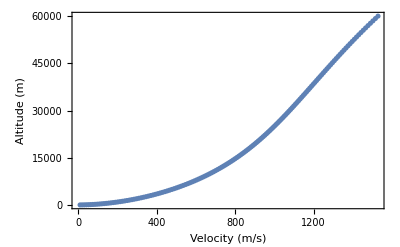

```mathematica
rocketGraph[.5,500,2750000,185000,5,1,9.8]
```

A plot for a single stage rocket without atmospheric drag or gravity

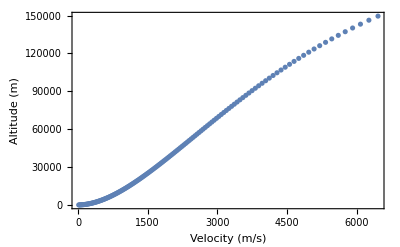

```mathematica
rocketGraph[.5,800,2750000,185000,5,0,0]
```

A plot for a singe stage rocket without atmospheric drag, but with gravity

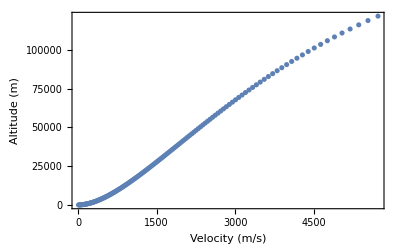

```mathematica
rocketGraph[.5,800,2750000,185000,5,0,9.8]
```

A plot for a single stage rocket with atmospheric drag, but no gravity. Note the lag in velocity as the rocket accelerates and that even though there is no gravity the rocket does not make it much higher than in the standard plot with drag and gravity.

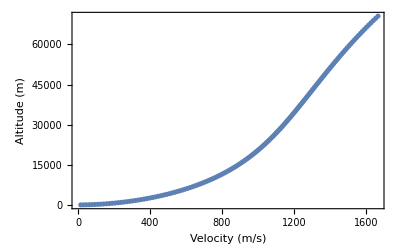

```mathematica
rocketGraph[.5,500,2750000,185000,5,1,0]
```

### Accuracy Testing

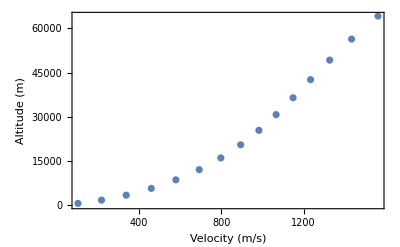

```mathematica
rocketGraph[5,500,2750000,185000,5,1,9.8]
```

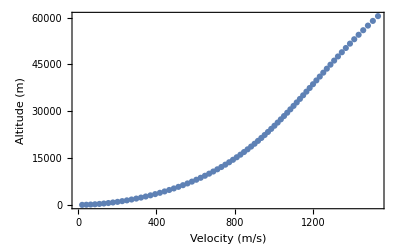

```mathematica
rocketGraph[1,500,2750000,185000,5,1,9.8]
```

```mathematica
rocketGraph[.5,500,2750000,185000,5,1,9.8]
```

-Graphics-

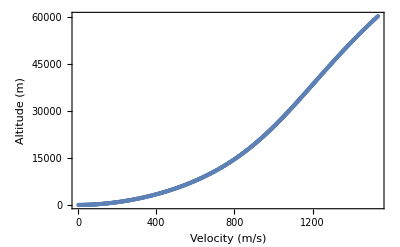

```mathematica
rocketGraph[.1,500,2750000,185000,5,1,9.8]
```

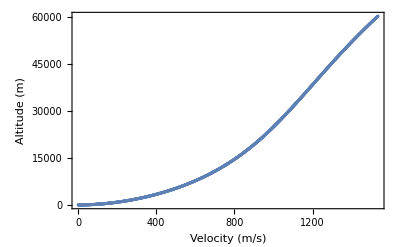

```mathematica
rocketGraph[.05,500,2750000,185000,5,1,9.8]
```

Commented out these calculations so that when you evaluate notebook these cells aren’t run. (They take some time)

```mathematica
(*rocketLive[5,500,2750000,185000,5,1,9.8]
rocketLive[1,500,2750000,185000,5,1,9.8]
rocketLive[.5,500,2750000,185000,5,1,9.8]
rocketLive[.1,500,2750000,185000,5,1,9.8]
rocketLive[.05,500,2750000,185000,5,1,9.8]
rocketLive[.001,500,2750000,185000,5,1,9.8]
rocketLive[.0001,500,2750000,185000,5,1,9.8]*)
```

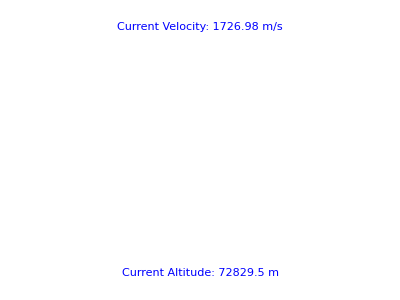

-Graphics-

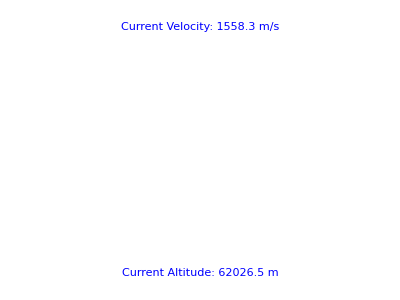

-Graphics-

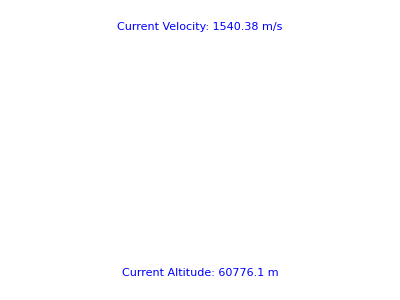

-Graphics-

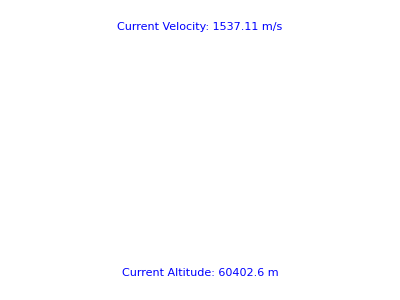

-Graphics-

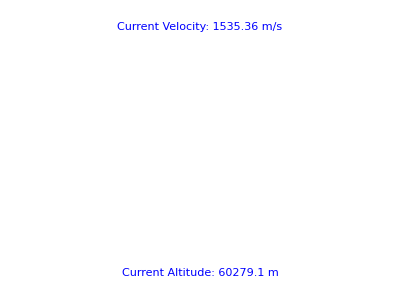

-Graphics-

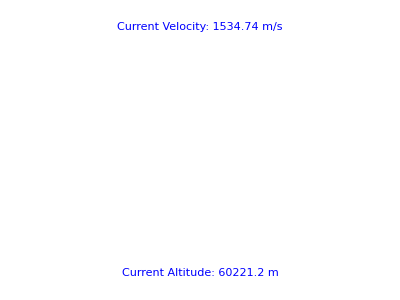

-Graphics-

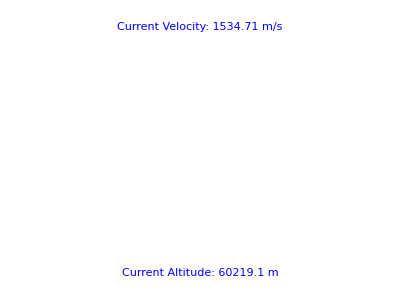

-Graphics-

```mathematica
(*rocketLive[.00001,500,2750000,185000,5,1,9.8]*)
```

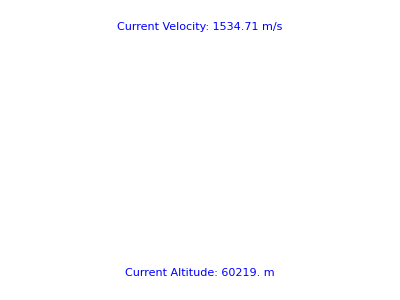

-Graphics-